-4+0.2 t+0.1 t^2-0.0002 t^3

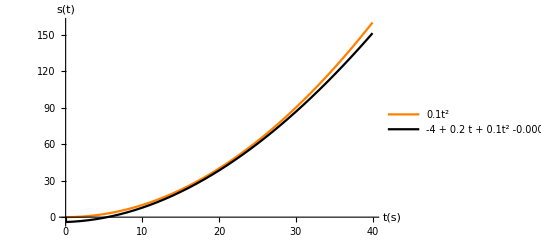

```mathematica
s1=0.1*t^2;
s2 = -4 + 0.2 t + 0.1t^2 -0.0002 t^3
table1 = Table[{t, s1},{t, 0,40,1}]; 
table2 = Table[{t, s2},{t, 0,40,1}]; 
ListPlot[{table1,table2},Joined->True,AxesLabel->{"t(s)","s(t)"}, PlotLegends->{"0.1t^2","-4 + 0.2 t + 0.1t^2 -0.0002 t^3"},LabelStyle->(FontSize->14),PlotStyle-> {Orange,Black, Thickness[0.00000001], Thickness[0.00000001]}]
```